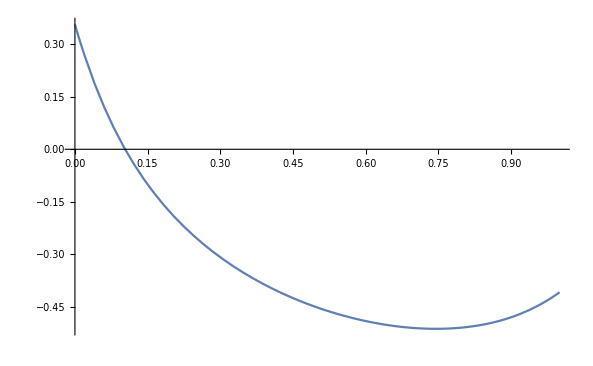

```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]];
data=Import["intervals.txt","Table"];


								(*ИСХОДНАЯ ФУНКЦИЯ*)

f[x_]:=-(Log[(-√3 x^4-x^2+5x+1)]/Log[10]+Tanh[(-x^5-2 x^4-x^3+3 x^2+6x+3-√5)/(x^2+2x+1)]-1);


							(*ГРАФИК ИСХОДНОЙ ФУНКЦИИ*)
Plot[f[x],{x,0,1}]
```

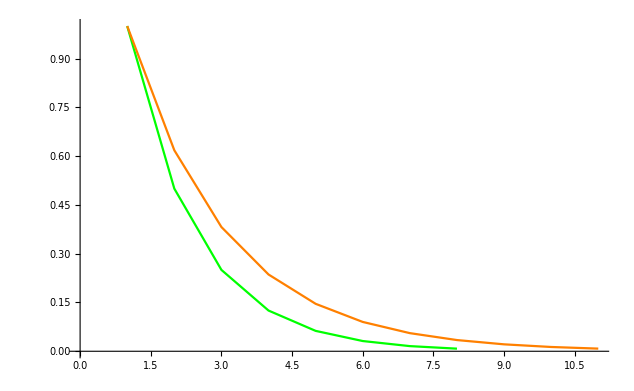

```mathematica
(*ИНТЕРВАЛЫ НЕОПРЕДЕЛЕННОСТИ ДЛЯ ТОЧНОСТИ EPS=0.01*)
dichotomyIntervals=data[[1]];
goldenRatioIntervals = data[[2]];
ListLinePlot[{dichotomyIntervals,goldenRatioIntervals},PlotStyle->{Green, Orange}]
```

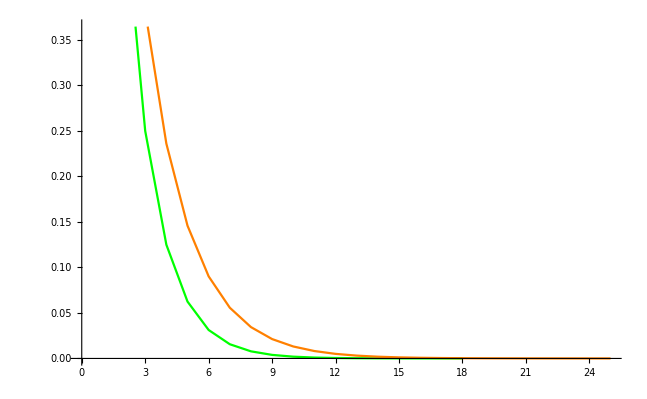

```mathematica
(*ИНТЕРВАЛЫ НЕОПРЕДЕЛЕННОСТИ ДЛЯ ТОЧНОСТИ EPS=0.00001*)
dichotomyIntervals=data[[3]];
goldenRatioIntervals = data[[4]];
ListLinePlot[{dichotomyIntervals,goldenRatioIntervals},PlotStyle->{Green, Orange}]
```

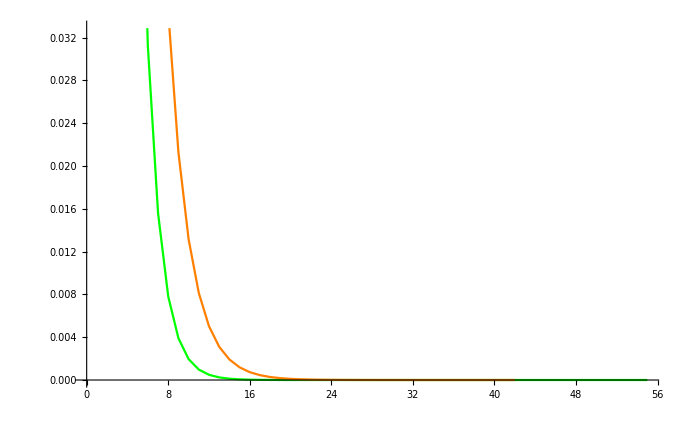

```mathematica
(*ИНТЕРВАЛЫ НЕОПРЕДЕЛЕННОСТИ ДЛЯ ТОЧНОСТИ EPS=0.00001*)
dichotomyIntervals=data[[5]];
goldenRatioIntervals = data[[6]];
ListLinePlot[{dichotomyIntervals,goldenRatioIntervals},PlotStyle->{Green, Orange}]
```